# Coulomb over een ribbon

## Eigenwaarden

```mathematica
ClearAll["Global`*"]
n = 75;
L = 1;
Ω = 1;
Remove[f]
f[n_, y_] := 1.0/; n == 0;
f[n_, y_] := Sqrt[2] * Cos[n*Pi*(y-1/2)] /; n ≠ 0;

Kern[k_, y1_,y2_] :=  (BesselK[0, k*Sqrt[(y1-y2)^2 + (0.0001)^2]]/Pi)


Lmn[k_] :=
ParallelTable[NIntegrate[f[i, y1]   * Kern[k,y1,y2] *  f[j, y2], {y1, -0.5, 0.5},{y2, -0.5, 0.5}, Method->{"GlobalAdaptive", "MaxErrorIncreases"->8000},MinRecursion->30,MaxRecursion->100, PrecisionGoal->3,AccuracyGoal->3],{i, 0, n}, {j,0,n} ]
Pmn[k_]:=Table[KroneckerDelta[i,j](k^2+i^2*Pi^2), {i, 0, n}, {j,0,n}]
```

```mathematica
Eigenvalues[Lmn[ 0.1] . Pmn[ 0.1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{27.7709,24.6254,21.4133,18.26,15.0717,11.9183,8.72867,5.58076,2.34315,0.0121696}

```mathematica
Dispersion = ParallelTable[Eigenvalues[Lmn[0.1*i].Pmn[0.1*i]], {i,1,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{27.7709,24.6254,21.4133,18.26,15.0717,11.9183,8.72867,5.58076,2.34315,0.0121696},{27.7714,24.6259,21.4138,18.2606,15.0724,11.9193,8.72954,5.58229,2.33886,0.0399131},{27.7721,24.6271,21.415,18.2618,15.0736,11.9209,8.73121,5.58485,2.33501,0.0783795},{27.7733,24.6283,21.4164,18.2634,15.0754,11.9232,8.73372,5.58848,2.33255,0.125101},{27.7747,24.63,21.4182,18.2656,15.0778,11.9262,8.73713,5.59321,2.33204,0.178446},{27.7765,24.632,21.4205,18.2681,15.0808,11.9298,8.74145,5.59906,2.33384,0.237228},{27.7787,24.6344,21.4231,18.2712,15.0843,11.9341,8.7467,5.60608,2.33818,0.300542},{27.7811,24.6371,21.4262,18.2748,15.0884,11.939,8.7529,5.61428,2.3452,0.367675},{27.7847,24.6403,21.4297,18.2788,15.0932,11.9447,8.76005,5.6237,2.35498,0.438051},{27.7879,24.6438,21.4337,18.2833,15.0985,11.951,8.76816,5.63437,2.36756,0.511199},{27.7914,24.6477,21.4381,18.2883,15.1044,11.958,8.77722,5.64631,2.38293,0.586729},{27.7952,24.6519,21.4429,18.2937,15.1108,11.9658,8.78726,5.65954,2.40107,0.664314},{27.7994,24.6566,21.4481,18.2997,15.1179,11.9743,8.79825,5.67409,2.42194,0.743678},{27.8039,24.6616,21.4538,18.3062,15.1256,11.9835,8.81022,5.68997,2.44548,0.824584},{27.8088,24.667,21.4599,18.3131,15.1339,11.9934,8.82315,5.70719,2.47162,0.906834},{27.814,24.6728,21.4665,18.3206,15.1428,12.004,8.83704,5.72577,2.50029,0.990255},{27.8195,24.679,21.4734,18.3285,15.1522,12.0154,8.8519,5.74572,2.53142,1.0747},{27.8254,24.6855,21.4808,18.337,15.1623,12.0274,8.86772,5.76704,2.56491,1.16003},{27.8316,24.6924,21.4887,18.346,15.1729,12.0402,8.8845,5.78974,2.60069,1.24615},{27.8382,24.6997,21.497,18.3554,15.1842,12.0538,8.90224,5.81382,2.63868,1.33294},{27.8451,24.7074,21.5057,18.3654,15.196,12.068,8.92094,5.83929,2.67878,1.42034},{27.8524,24.7155,21.5148,18.3758,15.2085,12.083,8.94059,5.86614,2.72092,1.50826},{27.86,24.724,21.5244,18.3868,15.2215,12.0988,8.96119,5.89437,2.76501,1.59663},{27.8679,24.7328,21.5344,18.3982,15.2351,12.1153,8.98274,5.92397,2.81098,1.68541},{27.8762,24.742,21.5448,18.4102,15.2493,12.1325,9.00523,5.95493,2.85874,1.77453},{27.8848,24.7516,21.5557,18.4227,15.2641,12.1504,9.02867,5.98725,2.90821,1.86396},{27.8938,24.7616,21.567,18.4357,15.2795,12.169,9.05304,6.02092,2.95934,1.95365},{27.9031,24.772,21.5787,18.4491,15.2955,12.1884,9.07834,6.05592,3.01203,2.04356},{27.9127,24.7828,21.5909,18.4631,15.3121,12.2086,9.10458,6.09225,3.06623,2.13368},{27.9227,24.7939,21.6034,18.4775,15.3292,12.2294,9.13174,6.12988,3.12187,2.22396},{27.9331,24.8054,21.6164,18.4925,15.347,12.251,9.15981,6.16881,3.17889,2.31439},{27.9437,24.8174,21.6299,18.508,15.3653,12.2733,9.1888,6.20902,3.23722,2.40494},{27.9547,24.8296,21.6438,18.5239,15.3842,12.2964,9.2187,6.2505,3.2968,2.4956},{27.9661,24.8423,21.6581,18.5405,15.4038,12.3201,9.24951,6.29321,3.35759,2.58634},{27.9778,24.8554,21.6728,18.5574,15.4238,12.3446,9.28121,6.33716,3.41952,2.67715},{27.9898,24.8688,21.688,18.5749,15.4445,12.3698,9.3138,6.38232,3.48255,2.76801},{28.0022,24.8826,21.7036,18.5929,15.4658,12.3956,9.34728,6.42867,3.54663,2.85892},{28.0149,24.8968,21.7196,18.6114,15.4876,12.4222,9.38164,6.47619,3.61171,2.94986},{28.0279,24.9114,21.7361,18.6302,15.51,12.4496,9.41686,6.52487,3.67774,3.04083},{28.0413,24.9264,21.753,18.6497,15.533,12.4776,9.45296,6.57469,3.74469,3.13181},{28.0558,24.9417,21.7703,18.6696,15.5566,12.5063,9.48991,6.62561,3.81251,3.2228},{28.0698,24.9575,21.788,18.6901,15.5807,12.5357,9.52772,6.67763,3.88117,3.3138},{28.0842,24.9736,21.8062,18.711,15.6054,12.5658,9.56637,6.73073,3.95062,3.40478},{28.099,24.99,21.8248,18.7325,15.6307,12.5966,9.60585,6.78487,4.02084,3.49575},{28.114,25.0069,21.8438,18.7543,15.6565,12.6281,9.64616,6.84006,4.09179,3.58671},{28.1295,25.0241,21.8632,18.7768,15.6829,12.6602,9.6873,6.89626,4.16344,3.67764},{28.1452,25.0417,21.8831,18.7997,15.7099,12.693,9.72924,6.95345,4.23576,3.76856},{28.1613,25.0597,21.9034,18.823,15.7374,12.7265,9.772,7.01162,4.30872,3.85946},{28.1777,25.0781,21.9241,18.8468,15.7655,12.7607,9.81555,7.07074,4.38229,3.95032},{28.1945,25.0968,21.9452,18.8711,15.7942,12.7955,9.85988,7.1308,4.45645,4.04115},{28.2116,25.116,21.9667,18.8959,15.8234,12.831,9.905,7.19177,4.53116,4.13195},{28.229,25.1354,21.9887,18.9212,15.8532,12.8672,9.95089,7.25364,4.60642,4.22271},{28.2467,25.1553,22.0111,18.947,15.8835,12.904,9.99754,7.31638,4.68219,4.31345},{28.2648,25.1755,22.0339,18.9732,15.9143,12.9414,10.0449,7.37999,4.75846,4.40414},{28.2833,25.1961,22.0571,19.,15.9457,12.9795,10.0931,7.44443,4.8352,4.49479},{28.302,25.2171,22.0807,19.0272,15.9777,13.0182,10.142,7.50969,4.91239,4.5854},{28.3211,25.2385,22.1047,19.0548,16.0101,13.0575,10.1916,7.57576,4.99003,4.67599},{28.3406,25.2602,22.1292,19.0829,16.0432,13.0975,10.2419,7.6426,5.06807,4.76654},{28.3603,25.2823,22.154,19.1115,16.0767,13.1381,10.293,7.71022,5.14653,4.85704},{28.3804,25.3047,22.1793,19.1406,16.1108,13.1793,10.3447,7.77858,5.22536,4.9475},{28.4008,25.3275,22.205,19.1701,16.1454,13.2211,10.3972,7.84768,5.30457,5.03793},{28.4216,25.3507,22.2311,19.2001,16.1806,13.2635,10.4503,7.91749,5.38413,5.12832},{28.4426,25.3743,22.2576,19.2306,16.2162,13.3066,10.5041,7.988,5.46404,5.21868},{28.4641,25.3982,22.2845,19.2615,16.2524,13.3502,10.5586,8.05918,5.54427,5.309},{28.4858,25.4225,22.3118,19.2928,16.2891,13.3944,10.6137,8.13104,5.62482,5.39929},{28.5078,25.4471,22.3395,19.3247,16.3263,13.4392,10.6695,8.20355,5.70568,5.48954},{28.5302,25.4721,22.3676,19.3569,16.3641,13.4846,10.7259,8.27668,5.78683,5.57976},{28.553,25.4975,22.3961,19.3897,16.4023,13.5305,10.7829,8.35044,5.86826,5.66995},{28.576,25.5232,22.425,19.4228,16.4411,13.577,10.8406,8.42481,5.94996,5.76009},{28.5994,25.5493,22.4543,19.4565,16.4803,13.6241,10.8989,8.49976,6.03192,5.85023},{28.6231,25.5757,22.484,19.4905,16.5201,13.6718,10.9578,8.57529,6.11414,5.94032},{28.6471,25.6025,22.5141,19.525,16.5603,13.72,11.0173,8.65138,6.1966,6.03039},{28.6714,25.6297,22.5446,19.56,16.6011,13.7687,11.0774,8.72802,6.27929,6.12042},{28.6961,25.6572,22.5755,19.5954,16.6423,13.818,11.138,8.80519,6.36221,6.21045},{28.721,25.6851,22.6068,19.6313,16.684,13.8678,11.1992,8.88288,6.44535,6.30042},{28.7463,25.7133,22.6384,19.6674,16.7262,13.9182,11.261,8.96108,6.5287,6.39042},{28.772,25.7418,22.6705,19.7041,16.7689,13.9691,11.3234,9.03978,6.61225,6.48037},{28.7979,25.7708,22.703,19.7413,16.8121,14.0206,11.3863,9.11896,6.696,6.57031},{28.8242,25.8,22.7358,19.7788,16.8557,14.0725,11.4497,9.19862,6.77994,6.6602},{28.8507,25.8297,22.769,19.8168,16.8998,14.125,11.5136,9.27872,6.86406,6.75011},{28.8776,25.8596,22.8026,19.8552,16.9444,14.1779,11.5781,9.35929,6.94837,6.83998},{28.9048,25.8899,22.8366,19.894,16.9894,14.2314,11.6431,9.44028,7.03284,6.92986},{28.9324,25.9206,22.871,19.9332,17.0349,14.2854,11.7086,9.5217,7.11748,7.01972},{28.9602,25.9516,22.9057,19.9729,17.0809,14.3398,11.7746,9.60354,7.20228,7.10955},{28.9884,25.983,22.9408,20.013,17.1273,14.3948,11.8411,9.68578,7.28724,7.19939},{29.0168,26.0146,22.9763,20.0535,17.1741,14.4502,11.9081,9.76842,7.37235,7.28921},{29.0456,26.0467,23.0122,20.0943,17.2214,14.5061,11.9756,9.85145,7.45761,7.37903},{29.0747,26.0791,23.0484,20.1357,17.2692,14.5625,12.0435,9.93484,7.54301,7.46885},{29.1041,26.1118,23.085,20.1774,17.3174,14.6193,12.1119,10.0186,7.62855,7.55864},{29.1338,26.1448,23.122,20.2195,17.366,14.6766,12.1807,10.1027,7.71422,7.64846},{29.1638,26.1782,23.1593,20.262,17.4151,14.7344,12.25,10.1872,7.80003,7.73826},{29.1942,26.2119,23.1971,20.3049,17.4646,14.7926,12.3197,10.272,7.88596,7.82805},{29.2248,26.246,23.2351,20.3482,17.5145,14.8513,12.3899,10.3572,7.97201,7.91783},{29.2557,26.2804,23.2736,20.3919,17.5649,14.9104,12.4605,10.4426,8.05819,8.00764},{29.287,26.3151,23.3124,20.436,17.6156,14.9699,12.5315,10.5284,8.14448,8.09745},{29.3185,26.3502,23.3515,20.4805,17.6668,15.0299,12.6029,10.6145,8.23088,8.18724},{29.3504,26.3856,23.391,20.5254,17.7184,15.0903,12.6748,10.7008,8.31739,8.27705},{29.3826,26.4213,23.4309,20.5706,17.7704,15.1512,12.747,10.7875,8.40402,8.36687},{29.415,26.4573,23.4711,20.6163,17.8229,15.2124,12.8196,10.8745,8.49074,8.45672},{29.4478,26.4937,23.5117,20.6623,17.8757,15.2741,12.8926,10.9617,8.57757,8.54654}}

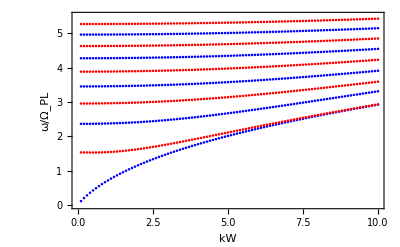

```mathematica
w0= Table[{0.1*i, Sqrt[Part[Dispersion,i,10]]}, {i,1,100}];
w1= Table[{0.1*i, Sqrt[Part[Dispersion,i,9]]}, {i,1,100}];
w2= Table[{0.1*i, Sqrt[Part[Dispersion,i,8]]}, {i,1,100}];
w3= Table[{0.1*i, Sqrt[Part[Dispersion,i,7]]}, {i,1,100}];
w4= Table[{0.1*i, Sqrt[Part[Dispersion,i,6]]}, {i,1,100}];
w5= Table[{0.1*i, Sqrt[Part[Dispersion,i,5]]}, {i,1,100}];
w6= Table[{0.1*i, Sqrt[Part[Dispersion,i,4]]}, {i,1,100}];
w7= Table[{0.1*i, Sqrt[Part[Dispersion,i,3]]}, {i,1,100}];
w8= Table[{0.1*i, Sqrt[Part[Dispersion,i,2]]}, {i,1,100}];
w9= Table[{0.1*i, Sqrt[Part[Dispersion,i,1]]}, {i,1,100}];

colFun[z_]:=If[z==Round[z],#,Black]&@If[EvenQ@Round@z,Red,Blue];

ListPlot[{Style[ w0, Blue] ,Style[ w1, Red],Style[ w2, Blue], Style[ w3, Red],Style[ w4, Blue],Style[ w5, Red],Style[ w6, Blue],Style[ w7, Red],Style[ w8, Blue],Style[ w9, Red]}, PlotRange->{{0,10},{0,5.5}}, BaseStyle->{FontSize->Scaled[.06]},Frame->True,FrameLabel->{{"ω/Ω_PL",""},{"kW",""}} ]
```

## Eigenfuncties Φ

```mathematica
kW = {0.1, 1,5,10,50};
For[i=1,i≤ Length[kW],i++, eigenVects[i] = Eigenvectors[Lmn[ Part[kW,i]] . Pmn[ Part[kW,i]]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

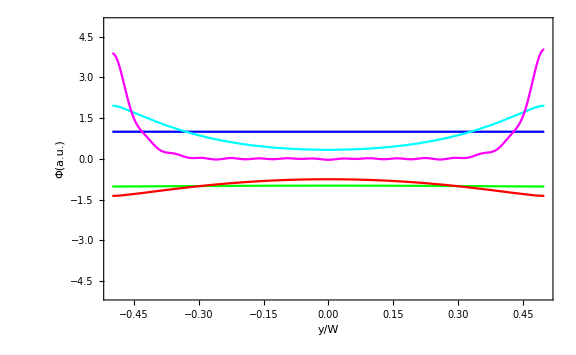
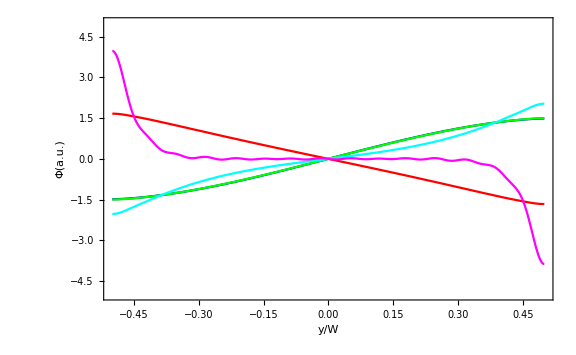
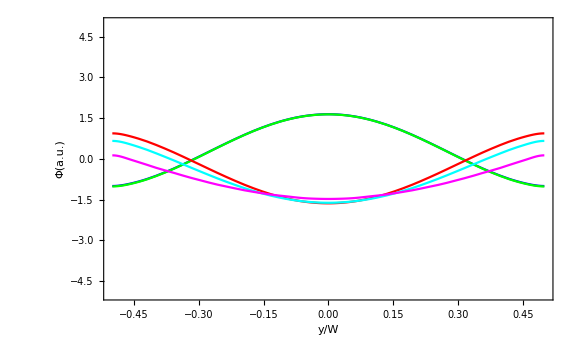
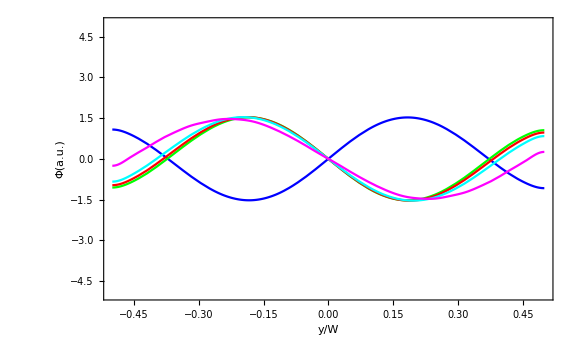

```mathematica
plots = Table[Plot[Evaluate@Table[ Sum[Part[eigenVects[j],n+1-l,(i+1)] f[i,y ] , {i,0,n}],{j,1,5}],{y,-0.5,0.5}, PlotRange->{-5,5},Frame->True,ImageSize->Large,ImageMargins->0,PlotRangePadding->0,  Frame->{True,True,False,False},FrameLabel->{Style["y/W",16,Bold],Style["Φ(a.u.)",16,Bold]} ,PlotTheme-> j, PlotStyle->{Blue,Green,Red,Cyan,Magenta}],{l,0,3}]
```

Ben Thesis p188 absorptie enzo

```mathematica
matrix = Lmn[ 0.0001] . Pmn[ 0.0001];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

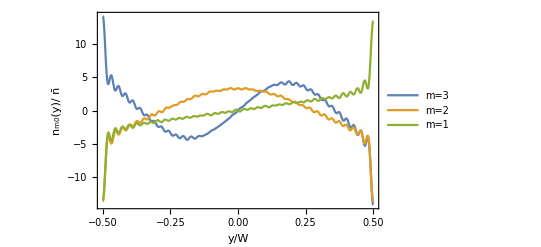

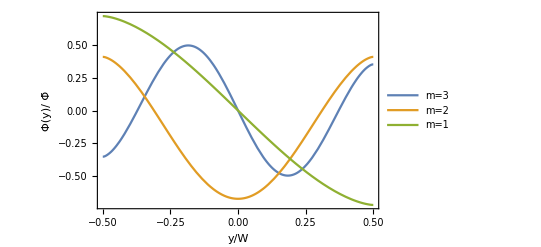

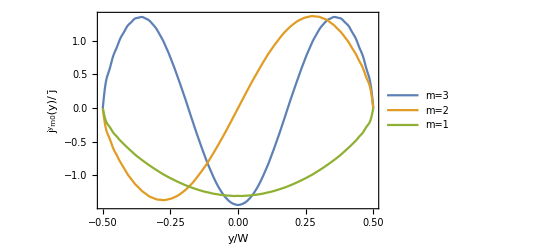

```mathematica
Plot[Evaluate@Table[(Sqrt[NIntegrate[-D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}]Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,-0.5,0.5}]])^-1 D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}],{j,n-2,n}],{y,-0.5,0.5},Frame->True,FrameLabel->{{Style["n_m0(y)/ n̄", FontSize->16],""},{Style["y/W", FontSize->16],""}} , PlotLegends->{"m=3","m=2","m=1"}]
Plot[Evaluate@Table[(Sqrt[NIntegrate[-D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}]Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,-0.5,0.5}]])^-1 Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{j,n-2,n}],{y,-0.5,0.5},Frame->True,FrameLabel->{{Style["Φ(y)/ Φ̄", FontSize->16],""},{Style["y/W", FontSize->16],""}} , PlotLegends->{"m=3","m=2","m=1"}]
Plot[Evaluate@Table[(Sqrt[NIntegrate[-D[1/(Eigenvalues[matrix][[j]])Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}]Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,-0.5,0.5}]])^-1 D[1/Sqrt[Eigenvalues[matrix][[j]]] Sum[Eigenvectors[matrix][[j]][[i]] f[i-1,y ] , {i,1,n+1}],{y,1}],{j,n-2,n}],{y,-0.5,0.5},Frame->True,FrameLabel->{{Style["(j^y)_m0(y)/ j̄", FontSize->16],""},{Style["y/W", FontSize->16],""}} , PlotLegends->{"m=3","m=2","m=1"}]
```

```mathematica
Export["Ribbon9jan_LmPm_N75_k0.0001.CSV", matrix,"CSV"]
```

Ribbon9jan_LmPm_N75_k0.0001.CSV

```mathematica
matrix = Import["Ribbon9jan_LmPm_N75_k0.0001.CSV"];
```

```mathematica
α= Monitor[Table[NIntegrate[y (Sqrt[NIntegrate[-D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}]Sum[Eigenvectors[matrix][[m]][[i]] f[i-1,y ] , {i,1,n}],{y,-0.5,0.5}]])^-1 D[1/(Eigenvalues[matrix][[m]])Sum[Eigenvectors[matrix][[m]][[i]] f[i-1,y ] , {i,1,n+1}],{y,2}], {y,-0.5,0.5}], {m,1,n+1}],m]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.4999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained -9.47538×10^-11 and 1.00822×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.4999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained 1.64607×10^-11 and 2.44963×10^-10 for the integral and error estimates.

{0.00317066,-2.66586×10^-8,-0.000395032,4.73056×10^-7,-0.000491932,2.77257×10^-7,-0.000591967,1.12519×10^-7,-0.000576795,5.41947×10^-8,-0.000654558,2.61467×10^-6,0.00064132,-4.16663×10^-8,-0.000725875,1.74699×10^-7,-0.000691248,-1.73007×10^-7,0.000718552,-9.24001×10^-8,0.000736095,-1.84635×10^-8,-0.000913813,-9.47538×10^-11,0.00097169,3.46483×10^-8,-0.000845326,3.80108×10^-7,0.00105849,-7.3375×10^-8,-0.00118874,-6.79238×10^-8,0.00122061,-1.77605×10^-7,0.00124046,-2.089×10^-7,0.00146997,-2.88587×10^-7,0.0017028,4.0073×10^-7,-1.00631×10^-6,-0.00166005,-0.00198737,0.0000413267,0.00200344,0.00232788,-1.4962×10^-8,7.65635×10^-8,0.00260744,-3.86844×10^-7,0.00271465,-2.92132×10^-8,-0.00328981,-1.10848×10^-7,-0.00367578,-6.52538×10^-7,-0.00441453,-1.04194×10^-7,0.00526468,-2.28242×10^-7,-0.00625407,-1.08805×10^-6,0.00792554,5.36647×10^-7,-0.0102291,-3.39488×10^-6,0.0140415,-6.18715×10^-8,-0.0206704,-1.63097×10^-6,0.0352587,1.23526×10^-6,-0.0810834,2.68435×10^-7,0.618441,-0.0887409}

```mathematica
α
```

{0.00317066,-2.66586×10^-8,-0.000395032,4.73056×10^-7,-0.000491932,2.77257×10^-7,-0.000591967,1.12519×10^-7,-0.000576795,5.41947×10^-8,-0.000654558,2.61467×10^-6,0.00064132,-4.16663×10^-8,-0.000725875,1.74699×10^-7,-0.000691248,-1.73007×10^-7,0.000718552,-9.24001×10^-8,0.000736095,-1.84635×10^-8,-0.000913813,-9.47538×10^-11,0.00097169,3.46483×10^-8,-0.000845326,3.80108×10^-7,0.00105849,-7.3375×10^-8,-0.00118874,-6.79238×10^-8,0.00122061,-1.77605×10^-7,0.00124046,-2.089×10^-7,0.00146997,-2.88587×10^-7,0.0017028,4.0073×10^-7,-1.00631×10^-6,-0.00166005,-0.00198737,0.0000413267,0.00200344,0.00232788,-1.4962×10^-8,7.65635×10^-8,0.00260744,-3.86844×10^-7,0.00271465,-2.92132×10^-8,-0.00328981,-1.10848×10^-7,-0.00367578,-6.52538×10^-7,-0.00441453,-1.04194×10^-7,0.00526468,-2.28242×10^-7,-0.00625407,-1.08805×10^-6,0.00792554,5.36647×10^-7,-0.0102291,-3.39488×10^-6,0.0140415,-6.18715×10^-8,-0.0206704,-1.63097×10^-6,0.0352587,1.23526×10^-6,-0.0810834,2.68435×10^-7,0.618441,-0.0887409}

```mathematica
Ω = 2.78*10^13* (1)^(1/4)/(√(2.75*0.02))
A[ω_] = Sum[(ω^2 α[[i]]^2 Eigenvalues[matrix][[i]])/((ω^2 - Ω^2 Eigenvalues[matrix][[i]])^2 + 0.3^2  Ω^2  ω^2), {i,1,n+1}] ;
```

1.1854×10^14

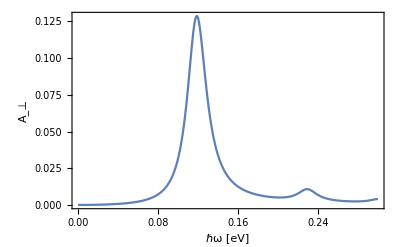

```mathematica
Plot[(2(2.78*10^13)^2 *0.3 Ω)/(3*10^14)A[ω*(6.58)^-1*10^16], {ω,0,0.3}, PlotRange->All,Frame->True,FrameLabel->{{Style["A__⊥", FontSize->16],""},{Style["ℏω [eV]", FontSize->16],""}}]
```

```mathematica
Sqrt[Eigenvalues[matrix]]
```

{15.1896,15.0883,14.9905,14.8832,14.7812,14.7005,14.5815,14.4674,14.3719,14.2582,14.1442,14.0691,13.9384,13.8432,13.7323,13.6154,13.5073,13.3957,13.2814,13.1369,13.0472,12.921,12.8047,12.6878,12.5639,12.4436,12.3197,12.1697,12.0646,11.9307,11.7986,11.6661,11.5357,11.4071,11.2822,11.141,10.994,10.8688,10.7082,10.6357,10.533,10.4346,10.1083,9.98754,9.80014,9.48507,9.3224,9.27735,9.15074,8.98771,8.81279,8.61494,8.44315,8.26215,8.06914,7.87577,7.67131,7.46959,7.25345,7.02503,6.80857,6.5641,6.33587,6.08529,5.81901,5.54181,5.24859,4.94071,4.61018,4.25324,3.86661,3.43618,2.94108,2.34951,1.52313,0.000184681}

```mathematica
α[3]
```

-0.000395032

```mathematica
Eigenvalues[matrix][[n+1]]
```

3.41071×10^-8